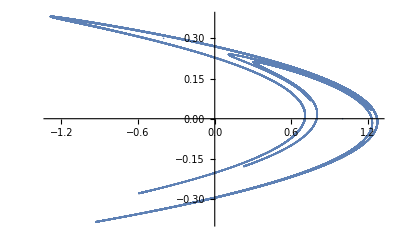

```mathematica
ClearAll[a, b, x,y,list, p1, henon]
a = 1.4;
b = 0.3;
henon[{x_, y_}] := {y+ 1 - a*x^2, b*x}
list = NestWhileList[henon, {0, 0},Max[Abs[#]]<20, 100000];
ListPlot[list]
```

1.23252

1.23387

1.23384

1.23281

1.23083

1.22781

1.2236

1.21798

1.21071

1.20152

1.19016

1.17646

1.16034

1.14193

1.12157

1.09978

1.07721

1.05452

1.03232

1.01106

0.991079

{{0.001,1.23252},{0.201,1.23387},{0.401,1.23384},{0.601,1.23281},{0.801,1.23083},{1.001,1.22781},{1.201,1.2236},{1.401,1.21798},{1.601,1.21071},{1.801,1.20152},{2.001,1.19016},{2.201,1.17646},{2.401,1.16034},{2.601,1.14193},{2.801,1.12157},{3.001,1.09978},{3.201,1.07721},{3.401,1.05452},{3.601,1.03232},{3.801,1.01106},{4.001,0.991079}}

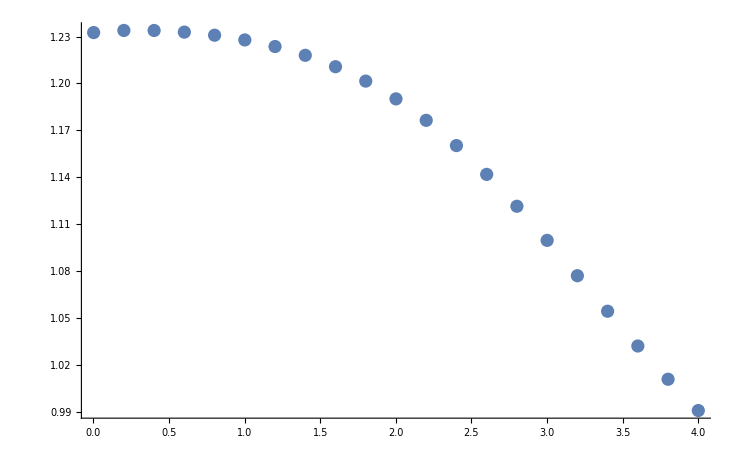

```mathematica
ClearAll[a, b, x,y,list, p1, henon, eps, q, bins, totalNbrOfDataPoints, pk]
a = 1.4;
b = 0.3;
henon[{x_, y_}] := {y+ 1 - a*x^2, b*x}
list = NestWhileList[henon, {0, 0},Max[Abs[#]]<20, 2000000];
list2 = NestWhileList[henon, {1, 0.1},Max[Abs[#]]<20, 100001];
list3 = NestWhileList[henon, {-1, 0.1},Max[Abs[#]]<20, 100001];
list4 = NestWhileList[henon, {1.3, 0.4}, Max[Abs[#]]<20, 100001];
dataPoints = Join[list[[100000;;-1]], list2[[100000;;-1]], list3[[100000;;-1]], list4[[100000;;-1]]];
calculateI[eps_,q_] :={bins=BinCounts[dataPoints , {-1.3,1.3,eps}, {-0.5,0.5,eps}];totalNbrOfDataPoints = Total[Total[bins]] ;pk = bins / totalNbrOfDataPoints//Flatten;pk = Select[pk, # > 0 &];Iqe = Total[pk^q];Iqe}
calculateD[q_]:={is=Table[{-Log[eps],Log[calculateI[eps,q][[1]]]},{eps,0.001,0.02,0.002}];slope=LinearModelFit[is,x,x][[1]][[2]][[2]];d=slope/(1-q);Print[d];d}
ds=Table[{q,calculateD[q][[1]]},{q, 0.001,4.001,0.2}]
ListPlot[ds]
```

```mathematica
calculateD1[eps_]:={bins=BinCounts[dataPoints , {-1.3,1.3,eps}, {-0.5,0.5,eps}];totalNbrOfDataPoints = Total[Total[bins]] ;
pk = bins / totalNbrOfDataPoints//Flatten;
pk = Select[pk, # > 0 &];
Total[pk * Log[pk]] / Log[eps]}
d1s=Table[{eps,calculateD1[eps][[1]]},{eps,0.0008,0.005,0.0004}]
ListPlot[Log[d1s]]
```

```mathematica
ListPlot[d1s]
LinearModelFit[d1s,x,x]
```

### exponents

```mathematica
ClearAll[a, b, x,y,list, p1, henon, eps, q, bins, totalNbrOfDataPoints, pk]
a = 1.4;
b = 0.3;
henon[{x_, y_}] := {y+ 1 - a*x^2, b*x}
nIterations=2*10^6;
list = NestWhileList[henon, {0, 0},Max[Abs[#]]<20, nIterations+100000];
list = list[[100001;;-1]];
lambdas = {0,0};
Q=IdentityMatrix[2];
jacobian[x_,y_] :={{-2*a*x,1},{b,0}};
Do[{x,y}=list[[i]];(M= jacobian[x,y];{Qnew,Rnew} = QRDecomposition[M.Q]; Q=Transpose[Qnew];lambdas+=Log[Abs[Diagonal[Rnew]]]/(nIterations);),{i,nIterations}];
Print["λ=",lambdas//MatrixForm]
Print["Dl= ",1-lambdas[[1]]/lambdas[[2]]]
```

λ=(0.419257
-1.62323)

Dl= 1.25829